# MM Analysis of Dichroic

## Kira Hart Polarization Lab, Wyant College of Optical Science University of Arizona

## Import and Format Data

```mathematica
data45 =  Import["/Users/kirahart/Dropbox/Research/Stepper/DichroicMM45.h5","mmVecs"];
data0   = Import["/Users/kirahart/Dropbox/Research/Stepper/DichroicMM0.h5","mmVecs"];
```

```mathematica
wavelengths = Subdivide[450,750,30];
```

Average MM

```mathematica
avg45 =Transpose[ Mean[Mean[data45]]];
avg0 = Transpose[Mean[Mean[data0]]];

std45 =Transpose[StandardDeviation[StandardDeviation[data45]]];
std0 = Transpose[StandardDeviation[StandardDeviation[data0]]];
```

```mathematica
getMM[data_, index_]:= ArrayReshape[data[[index]],{4,4}]
```

The next function will create a list of MMs where there are N number of MMs per wavelength where N is the number of spatial samples

```mathematica
getMMlist[data_]:=Module[{d,mms},
d=Flatten[data,1];
mms=Table[ArrayReshape[d[[;;,;;,i]],{100,4,4}],{i,1,31}];
Return[mms]];
```

```mathematica
mmlist45 =getMMlist[data45];
mmlist0 = getMMlist[data0];
```

## Mueller Matrix Plots

#### Mueller Elements vs. Wavelength

```mathematica
labels = {"m00","m01","m02","m03","m10","m11","m12","m13","m20","m21","m22","m23","m30","m31","m32","m33"};
```

```mathematica
mmelementplot[avg45_,avg0_,std45_,std0_,i_]:= Module[{d45,d0,range},
d45 = Table[{wavelengths[[j]],Around[avg45[[j,i]],std45[[j,i]]]},{j,1,31}];
d0 = Table[{wavelengths[[j]],Around[avg0[[j,i]],std0[[j,i]]]},{j,1,31}];
If[i ==1,range ={0,1},range = {-1,1}];
ListPlot[{d45,d0},PlotTheme->"Monochrome",Frame->True,PlotRange->{All,range},FrameLabel->{"Wavelength (nm)",labels[[i]]},PlotStyle->{{PointSize[.01]},{PointSize[.01]}}(*,PlotLegends->{"AOI = 45 °","AOI = 0 °"}*),LabelStyle->{FontFamily->"Arial",FontSize->12,Black},Joined->True,Epilog->{Directive[{Red,Dashed}],Line[{{650,-1},{1,650}}]}]]
```

#### PLot

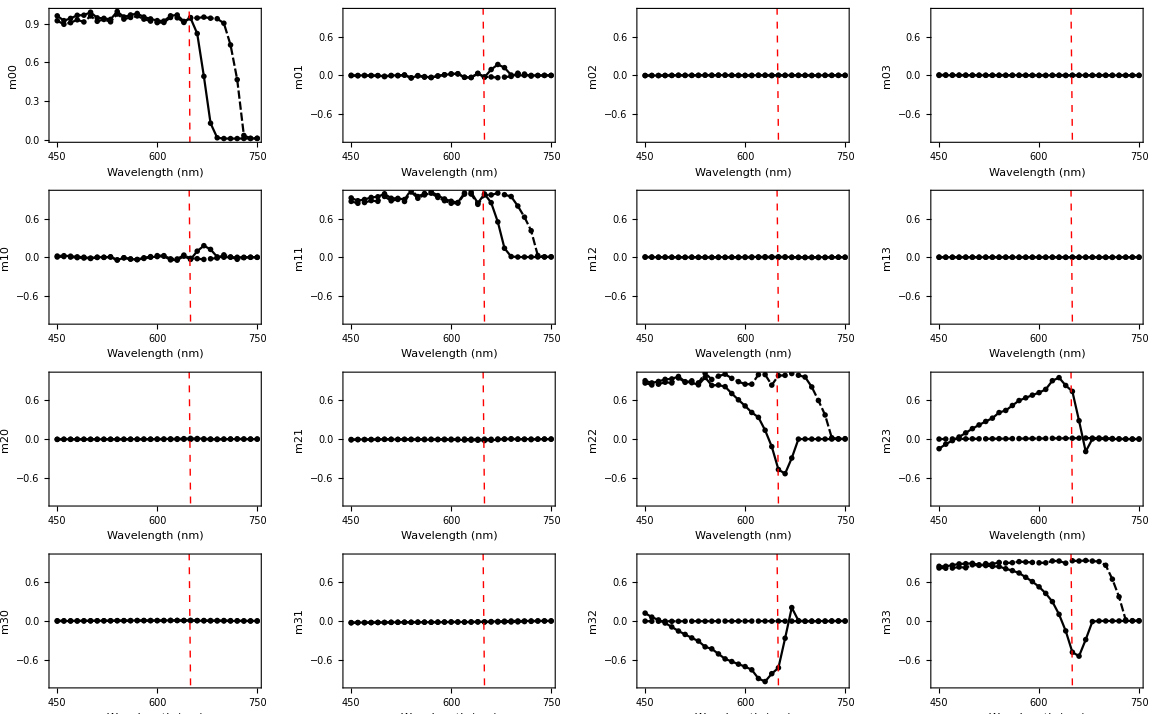

```mathematica
GraphicsGrid[{Table[mmelementplot[avg45,avg0,std45,std0,i],{i,1,4}],Table[mmelementplot[avg45,avg0,std45,std0,i],{i,5,8}],Table[mmelementplot[avg45,avg0,std45,std0,i],{i,9,12}],Table[mmelementplot[avg45,avg0,std45,std0,i],{i,13,16}]}]
```

#### Reduce Mueller Table

```mathematica
MuellerTable[data_,index_]:=Module[{output},
output=ReduceMueller[getMM[data,index]];
TableForm[{{output[[1,1]]//MatrixForm,output[[1,2]]//MatrixForm,output[[1,3]]//MatrixForm}},TableSpacing->{2,2},TableHeadings->{{"Vector","Reduced"},{"Diattentuation","Polarizance","Retardance"}}]];
```

```mathematica
MuellerTable[avg0,4]
```

| Diattentuation | Polarizance | Retardance
Vector | (-0.00594294
-0.00211643
0.00383217) | (-0.0071296
-0.00351768
0.00154577) | (0.00408315
-0.0148111
0.00613778)

#### Diattenuation Vector (pg. 178, eqn. 6.44)

```mathematica
diatVecs45 = Table[ReduceMueller[getMM[avg45,i]][[1,1]],{i,1,31}];
diatVecs0= Table[ReduceMueller[getMM[avg0,i]][[1,1]],{i,1,31}];
```

```mathematica
Diattenuation[]
```

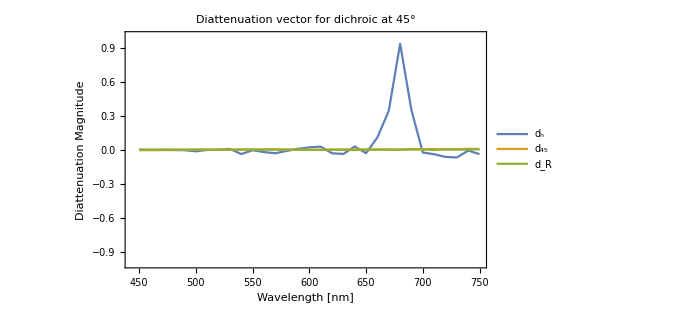

```mathematica
ListLinePlot[Table[Table[{wavelengths[[i]],Transpose[diatVecs45 ][[j,i]]},{i,1,31}],{j,1,3}],Frame->True,PlotStyle->PointSize[Medium],PlotRange->{All,{-1,1}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},PlotLegends->Placed[{"d_h","d_45","d_R"},{0.1,0.8}],FrameLabel->{"Wavelength [nm]","Diattenuation Magnitude"},PlotLabel->"Diattenuation vector for dichroic at 45°"]
```

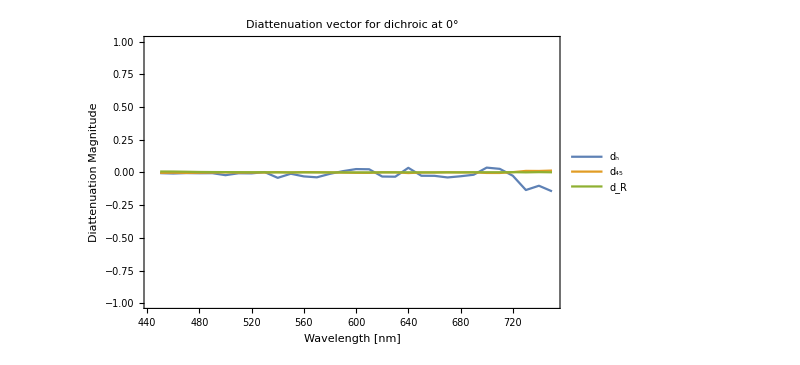

```mathematica
ListLinePlot[Table[Table[{wavelengths[[i]],Transpose[diatVecs0 ][[j,i]]},{i,1,31}],{j,1,3}],Frame->True,PlotStyle->PointSize[Medium],PlotRange->{All,{-1,1}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},PlotLegends->Placed[{"d_h","d_45","d_R"},{0.1,0.8}],FrameLabel->{"Wavelength [nm]","Diattenuation Magnitude"},PlotLabel->"Diattenuation vector for dichroic at 0°"]
```

#### Diattenuation Magnitude

```mathematica
diat[d_] := √(d[[1]]^2+d[[2]]^2+d[[3]]^2)
```

```mathematica
getDiatenuation[mmlist_,i_]:=Module[{dvecs,di},
dvecs=Map[ReduceMueller,mmlist[[i]]][[;;,1,1]];
di = Map[diat,dvecs];
Return[Around[Mean[di],StandardDeviation[di]]]
]
```

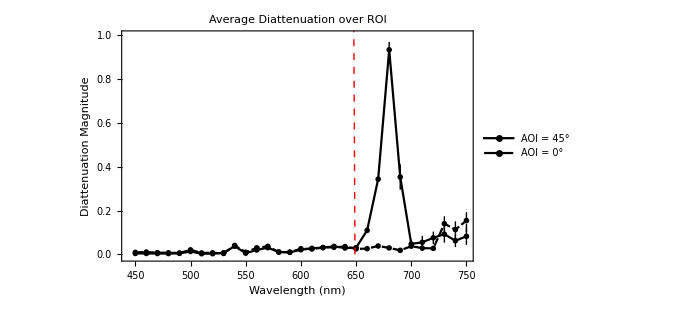

```mathematica
ListLinePlot[{Table[{wavelengths[[j]],getDiatenuation[mmlist45,j]},{j,1,31}],Table[{wavelengths[[j]],getDiatenuation[mmlist0,j]},{j,1,31}]},Frame->True,PlotStyle->PointSize[Medium],PlotRange->{All,{-.01,1}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},PlotLegends->Placed[{"AOI = 45°","AOI = 0°"},{0.2,0.8}],FrameLabel->{"Wavelength (nm)","Diattenuation Magnitude"},PlotLabel->"Average Diattenuation over ROI ",PlotTheme->"Monochrome",Epilog->{Directive[{Red,Dashed}],Line[{{650,-1},{1,650}}]},ImageSize->500]
```

#### Retardance Vector (page 171, eqn. 6.27)

```mathematica
retVecs45 = Table[ReduceMueller[getMM[avg45,i]][[1,3]],{i,1,31}];
retVecs0= Table[ReduceMueller[getMM[avg0,i]][[1,3]],{i,1,31}];
```

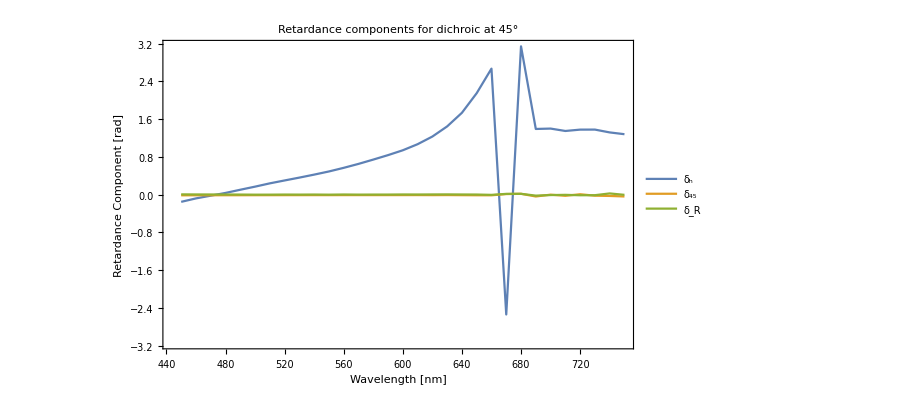

```mathematica
ListLinePlot[Table[Table[{wavelengths[[i]],Transpose[retVecs45 ][[j,i]]},{i,1,31}],{j,1,3}],Frame->True,PlotStyle->PointSize[Medium],PlotRange->{All,{-π,π}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},PlotLegends->Placed[{"δ_h","δ_45","δ_R"},{0.1,0.8}],FrameLabel->{"Wavelength [nm]","Retardance Component [rad]"},PlotLabel->"Retardance components for dichroic at 45°"]
```

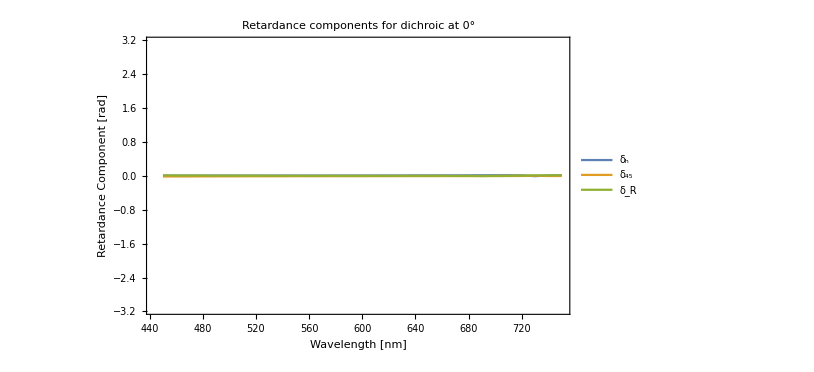

```mathematica
ListLinePlot[Table[Table[{wavelengths[[i]],Transpose[retVecs0 ][[j,i]]},{i,1,31}],{j,1,3}],Frame->True,PlotStyle->PointSize[Medium],PlotRange->{All,{-π,π}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},PlotLegends->Placed[{"δ_h","δ_45","δ_R"},{0.1,0.8}],FrameLabel->{"Wavelength [nm]","Retardance Component [rad]"},PlotLabel->"Retardance components for dichroic at 0°"]
```

#### Retardance Magnitude

```mathematica
getRetardance[mmlist_,i_]:=Module[{dvecs,di},
dvecs=Map[ReduceMueller,mmlist[[i]]][[;;,1,3]];
di = Map[diat,dvecs];
Return[Around[Mean[di],StandardDeviation[di]]]
]
```

```mathematica
ListLinePlot[{Table[{wavelengths[[j]],getRetardance[mmlist45,j]},{j,1,31}],Table[{wavelengths[[j]],getRetardance[mmlist0,j]},{j,1,31}]},Frame->True,PlotStyle->PointSize[Medium],PlotRange->{All,{-.1,π}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},PlotLegends->Placed[{"AOI = 45°","AOI = 0°"},{0.2,0.8}],FrameLabel->{"Wavelength (nm)","Retardance Magnitude (rad)"},PlotLabel->"Average Retardance over ROI ",PlotTheme->"Monochrome",Epilog->{Directive[{Red,Dashed}],Line[{{650,-1},{1,650}}]},ImageSize->500]
```

#### Polarizance Magnitude

```mathematica
getPolarizance[mmlist_,i_]:=Module[{dvecs,di},
dvecs=Map[ReduceMueller,mmlist[[i]]][[;;,1,2]];
di = Map[diat,dvecs];
Return[Around[Mean[di],StandardDeviation[di]]]
]
```

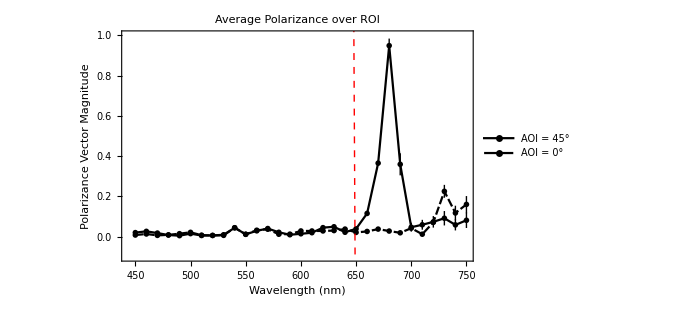

```mathematica
ListLinePlot[{Table[{wavelengths[[j]],getPolarizance[mmlist45,j]},{j,1,31}],Table[{wavelengths[[j]],getPolarizance[mmlist0,j]},{j,1,31}]},Frame->True,PlotStyle->PointSize[Medium],PlotRange->{All,{-.1,1}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},PlotLegends->Placed[{"AOI = 45°","AOI = 0°"},{0.2,0.8}],FrameLabel->{"Wavelength (nm)","Polarizance Vector Magnitude"},PlotLabel->"Average Polarizance over ROI ",PlotTheme->"Monochrome",Epilog->{Directive[{Red,Dashed}],Line[{{650,-1},{1,650}}]},ImageSize->500]
```

#### Depolarization

```mathematica
getDepolarization[mmlist_,i_]:=Module[{dvecs,di},
di=Map[DepIndex,mmlist[[i]]];
Return[Around[Mean[di],StandardDeviation[di]]]
]
```

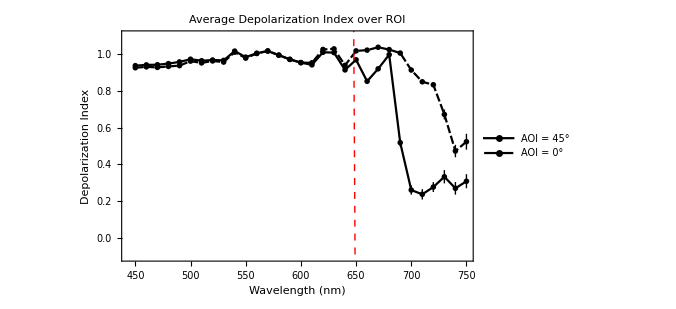

```mathematica
ListLinePlot[{Table[{wavelengths[[j]],getDepolarization[mmlist45,j]},{j,1,31}],Table[{wavelengths[[j]],getDepolarization[mmlist0,j]},{j,1,31}]},Frame->True,PlotStyle->PointSize[Medium],PlotRange->{All,{-.1,1.1}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},PlotLegends->Placed[{"AOI = 45°","AOI = 0°"},{0.2,0.7}],FrameLabel->{"Wavelength (nm)","Depolarization Index"},PlotLabel->"Average Depolarization Index over ROI ",PlotTheme->"Monochrome",Epilog->{Directive[{Red,Dashed}],Line[{{650,-1},{1,650}}]},ImageSize->500]
```

#### Operation on incident states

```mathematica
outputStokes[mmlist_, sin_]:=Module[{sout,s0,s1,s2,s3},
sout=Table[Map[Dot[#,sin]&,mmlist[[i]]],{i,1,31}];
s0 = Table[{wavelengths[[i]],Around[Mean[sout[[i]]][[1]],StandardDeviation[sout[[i]]][[1]]]},{i,1,31}];
s1 = Table[{wavelengths[[i]],Around[Mean[sout[[i]]][[2]],StandardDeviation[sout[[i]]][[2]]]},{i,1,31}];
s2 = Table[{wavelengths[[i]],Around[Mean[sout[[i]]][[3]],StandardDeviation[sout[[i]]][[3]]]},{i,1,31}];
s3 = Table[{wavelengths[[i]],Around[Mean[sout[[i]]][[4]],StandardDeviation[sout[[i]]][[4]]]},{i,1,31}];
Return[{s0,s1,s2,s3}]]
```

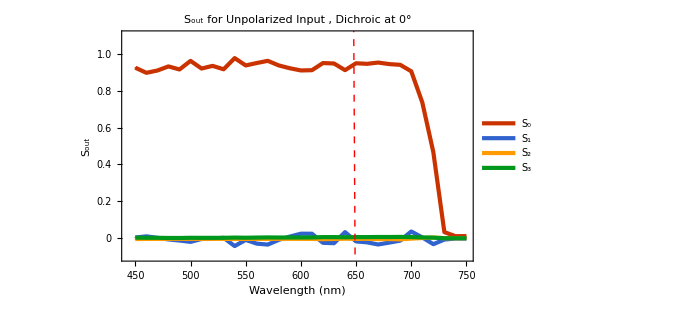

```mathematica
ListLinePlot[outputStokes[mmlist0,{1,0,0,0}],Frame->True,PlotStyle->PointSize[Medium],PlotRange->{All,{-.1,1.1}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},PlotLegends->Placed[{"S_0","S_1","S_2","S_3"},{0.2,0.5}],FrameLabel->{"Wavelength (nm)","S_out"},PlotLabel->"S_out for Unpolarized Input , Dichroic at 0°",PlotTheme->"Web",Epilog->{Directive[{Red,Dashed}],Line[{{650,-1},{1,650}}]},ImageSize->500]
```

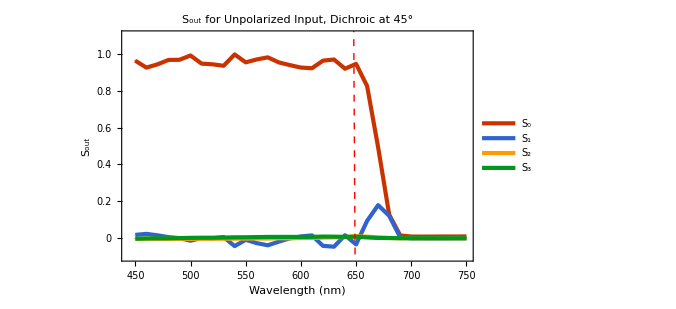

```mathematica
ListLinePlot[outputStokes[mmlist45,{1,0,0,0}],Frame->True,PlotStyle->PointSize[Medium],PlotRange->{All,{-.1,1.1}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},PlotLegends->Placed[{"S_0","S_1","S_2","S_3"},{0.2,0.5}],FrameLabel->{"Wavelength (nm)","S_out"},PlotLabel->"S_out for Unpolarized Input, Dichroic at 45°",PlotTheme->"Web",Epilog->{Directive[{Red,Dashed}],Line[{{650,-1},{1,650}}]},ImageSize->500]
```

## Conversion to Jones Matrix

#### Mueller Decomposition

```mathematica
MMdecompTable[data_,i_]:= Module[{DepolMM,RetMM,DiatMM},{DepolMM,RetMM,DiatMM}=DecomposeMueller[getMM[data, i]]//Chop;
TableForm[{{DepolMM//MatrixForm},{RetMM//MatrixForm},{DiatMM//MatrixForm}},TableHeadings->{{"Depolarization","Retardance","Diattenuation"},{"\t\tMatrix"}}]];
```

```mathematica
MMdecompTable[avg45,25]
```

| 		Matrix
Depolarization | (1. | 0 | 0 | 0
0.133492 | 0.632865 | -0.00543892 | -0.017079
0.000191515 | -0.00543892 | 0.190792 | -0.0411647
0.0171876 | -0.017079 | -0.0411647 | 0.149097)
Retardance | (1. | 0 | 0 | 0
0 | 0.99914 | -0.0384974 | 0.0154076
0 | -0.00827994 | 0.178864 | 0.983839
0 | -0.0406311 | -0.98312 | 0.178391)
Diattenuation | (0.0150185 | 0.00522218 | 0.0000907861 | 0.0000394004
0.00522218 | 0.0150182 | 0.0000162924 | 7.07075×10^-6
0.0000907861 | 0.0000162924 | 0.0140813 | 1.22923×10^-7
0.0000394004 | 7.07075×10^-6 | 1.22923×10^-7 | 0.0140811)

### Mueller to Jones via Coherency Matrix

#### Example Calculation

```mathematica
coh=MuellerToCoherency[getMM[avg0, 20]];
HermitianMatrixQ[coh]
```

True

```mathematica
coh//MatrixForm
```

(0.44956 | -0.00158735+0.0000213279 ⅈ | -0.00141561-0.00249083 ⅈ | 0.43429-0.00372707 ⅈ
-0.00158735-0.0000213279 ⅈ | 0.0226054 | -0.0148066+0.00223944 ⅈ | 0.000131914+0.00509938 ⅈ
-0.00141561+0.00249083 ⅈ | -0.0148066-0.00223944 ⅈ | 0.0222449 | -0.000515173-0.00061889 ⅈ
0.43429+0.00372707 ⅈ | 0.000131914-0.00509938 ⅈ | -0.000515173+0.00061889 ⅈ | 0.416834)

```mathematica
{U,d,V}=SingularValueDecomposition[coh];
```

```mathematica
U.d.Conjugate[Transpose[V]]//MatrixForm
U.d.Conjugate[Transpose[U]]//MatrixForm
```

(0.44956+3.00241×10^-20 ⅈ | -0.00158735+0.0000213279 ⅈ | -0.00141561-0.00249083 ⅈ | 0.43429-0.00372707 ⅈ
-0.00158735-0.0000213279 ⅈ | 0.0226054-3.67358×10^-18 ⅈ | -0.0148066+0.00223944 ⅈ | 0.000131914+0.00509938 ⅈ
-0.00141561+0.00249083 ⅈ | -0.0148066-0.00223944 ⅈ | 0.0222449-3.81694×10^-18 ⅈ | -0.000515173-0.00061889 ⅈ
0.43429+0.00372707 ⅈ | 0.000131914-0.00509938 ⅈ | -0.000515173+0.00061889 ⅈ | 0.416834-6.49674×10^-19 ⅈ)

(0.451502+0. ⅈ | -0.00134453-0.000396534 ⅈ | -0.0012357-0.00251705 ⅈ | 0.432272-0.00371239 ⅈ
-0.00134453+0.000396534 ⅈ | 0.0227257+0. ⅈ | -0.0147784+0.00227488 ⅈ | -0.000123589+0.00466697 ⅈ
-0.0012357+0.00251705 ⅈ | -0.0147784-0.00227488 ⅈ | 0.0222619+2.16417×10^-19 ⅈ | -0.00070234-0.000644777 ⅈ
0.432272+0.00371239 ⅈ | -0.000123589-0.00466697 ⅈ | -0.00070234+0.000644777 ⅈ | 0.418931-2.11758×10^-21 ⅈ)

```mathematica
d
```

{{0.867831,0.,0.,0.},{0.,0.037859,0.,0.},{0.,0.,0.00764154,0.},{0.,0.,0.,0.00208806}}

```mathematica
d
```

{{0.867831,0.,0.,0.},{0.,0.037859,0.,0.},{0.,0.,0.00764154,0.},{0.,0.,0.,0.00208806}}

```mathematica
d2 = {{d[[1,1]],0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
```

```mathematica
d2 ={{0.8678313907517107,0.,0.,0.},{0.,0,0.,0.},{0.,0.,0,0.},{0.,0.,0.,0}};
```

```mathematica
coh2= U.d2.ConjugateTranspose[U]
```

{{0.450233+0. ⅈ,-0.000785496-0.00258558 ⅈ,-0.000994571-0.000963438 ⅈ,0.433582-0.00372792 ⅈ},{-0.000785496+0.00258558 ⅈ,0.0000162187+0. ⅈ,7.26796×10^-6-4.03073×10^-6 ⅈ,-0.000735038+0.00249646 ⅈ},{-0.000994571+0.000963438 ⅈ,7.26796×10^-6+4.03073×10^-6 ⅈ,4.25865×10^-6-4.23516×10^-22 ⅈ,-0.000949813+0.000936043 ⅈ},{0.433582+0.00372792 ⅈ,-0.000735038-0.00249646 ⅈ,-0.000949813-0.000936043 ⅈ,0.417578+0. ⅈ}}

```mathematica
newMM=CoherencyToMueller[coh2];
newMM//MatrixForm//Chop
```

(0.867831 | 0.0326423 | -0.00347062 | 0.00329907
0.0326663 | 0.86779 | 0.000328635 | 0.00704324
-0.00345922 | -0.000519067 | 0.867179 | 0.00744778
0.00306605 | -0.0069198 | -0.00746391 | 0.86715)

```mathematica
DepIndex[getMM[avg45, 20]]
```

0.912512

```mathematica
MuellerToJones[newMM]//MatrixForm
```

(0.943771-0.00405718 ⅈ | -0.00162325+0.00542693 ⅈ
-0.00207613+0.00202851 ⅈ | 0.908902+0.00390728 ⅈ)

```mathematica
wavelengths[[20]]
```

640

#### Define Functions

```mathematica
returnMuellerAndJones[MM_]:= Module[{coh,U,d,V,d2,coh2,newMM,jones},
coh=MuellerToCoherency[MM]; (*generate coherency matrix from input jones*)
{U,d,V}=SingularValueDecomposition[coh];(*take SVD*)
d2 = {{d[[1,1]],0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}; (*only take largest singular value*)
coh2= U.d2.ConjugateTranspose[U]; (*form new coherency matrix*)
newMM=CoherencyToMueller[coh2]; (*form new non-depol Mueller Matrix*)
jones =MuellerToJones[newMM]; (*make Jones*)
Return[{newMM//Chop,jones//Chop}]];
```

```mathematica
returnMuellerAndJones[getMM[avg45,1]]
```

{{{0.915362,0.0100683,-0.00388817,-0.00107926},{0.0100274,0.915242,0.00570217,0.0130236},{-0.00371845,-0.00369049,0.904594,-0.139573},{-0.0018104,-0.0137597,0.13951,0.9045}},{{0.959135+0.0735462 ⅈ,0.000465452+0.0062623 ⅈ},{-0.00445848+0.00777488 ⅈ,0.948664-0.0727432 ⅈ}}}